This is not really an assignment (as far as assignment grading goes), but I am requiring you to complete your task listed here by the Monday after Oct. break, Oct. 29. That is two weeks from now. I would imagine that some or all of of you will do a little more than is asked for here. And of course, if questions arise on coding, etc., do ask. 

We will be starting presentations.....  well, last class day is Dec. 10, which I would like to reserve. Therefore there are 3 class days in Dec. for 6 of you...  and 2 more in November for 4 more:  This means Nov 26 and Nov 24. So that is less than a month away from this assignment due date. So work has to begin in earnest now.


Project Time:  A Customized Assignment.

### Jenna

Make up a simulated season of 10 teams and assume 70% of the games have been played. Form the network and figure out which teams can still win the championship. Here is code that makes up a random season. (You might need to vary the numbers for your purposes.

```mathematica
n=5;
games=List@@@EdgeList[CompleteGraph[5]]  (* sneakily avoiding Table, etc *) 
seasonAll=Join@@Table[games, {4 n}];  (* each game occurs four times *) 
played = RandomSample[seasonAll,Round[ 0.7 Length[seasonAll]]];
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}

```mathematica
results=Table[Append[p, p[[RandomInteger[{1,2}]]]], {p, played}];
results[[5]]
```

{1,3,1}

This means that in the 5th game in the list, team 1 won.

You can use the FindMaximumFlowLP function in Graphs469 package.

### Malcolm

Malcolm: Not sure. Show me something new relevant to your project; and perhaps outline your plan, and start some coding.

### Eric

Given that paper you found:  

A description of the algorithm you intend to program.
If appropriate, a by-hand computation of a toy example. If not, start in on a real example...

### Ben

Write a program that accepts some points and a cycle (of indices) with duplicates, and eliminates the duplicates in a greedy way based on the distance saved by the shortcutting. Here are some sample points and a cycle with dups.

```mathematica
SeedRandom[1]; pts = RandomReal[1, {10,2}]
```

{{0.817389,0.11142},{0.789526,0.187803},{0.241361,0.0657388},{0.542247,0.231155},{0.396006,0.700474},{0.211826,0.748657},{0.422851,0.247495},{0.977172,0.825163},{0.925275,0.578056},{0.29287,0.208051}}

```mathematica
SeedRandom[2]; cy=RandomChoice[Range[10], {30}]
```

{9,5,6,5,8,5,1,2,1,5,4,8,4,1,3,8,9,8,10,4,7,3,4,9,10,2,4,9,6,6}

### Megan

Your first order of business might be to work out a very simple example by hand. Summarize what the basic algorithm is? And show what the network looks like for a small example.

### Nick

Use the “all maximal independent set” method (the “static” method) to make an ILP setup that will yield the chromatic number and also the fractional chromatic number of the following graph. Use my MaximalIndependentSets function to get all the maximal independent sets for this graph. There are only 16. Once this is working, try a larger graph too.

```mathematica
g=GraphData["GolombGraph"]
VertexList[g]
EdgeList[g]
```

-Graphics-

{1,2,3,4,5,6,7,8,9,10}

{1<->2,1<->3,1<->4,2<->3,2<->6,3<->8,4<->5,4<->9,4<->10,5<->6,5<->10,6<->7,6<->10,7<->8,7<->10,8<->9,8<->10,9<->10}

```mathematica
<<Graphs469`
MaximalIndependentSets[g]
```

{{1,5,7,9},{1,5,8},{1,6,8},{1,6,9},{1,10},{2,4,7},{2,4,8},{2,5,7,9},{2,5,8},{2,10},{3,4,6},{3,4,7},{3,5,7,9},{3,9,6},{3,10},{4,6,8}}

### Yu

Work out a small example of the VRP routing problem. Just use two trucks and let all demands and capacities be 1. Here is a sample problem.

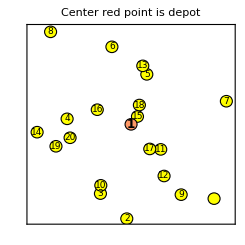

```mathematica
SeedRandom[3];pts=Prepend[RandomReal[1, {20,2}], {.5,.5}];
Graphics[{PointSize[.02], EdgeForm[Black],Yellow, Disk[#,.03]& /@Rest@pts,PointSize[.04], RGBColor[1,0.6,0.4],Disk[pts[[1]], .03],
{Black, Table[Text[Style[i,9], pts[[i]]], {i, 2,20}],
Text[Style[1,12,Bold], pts[[1]]]}}, Frame->True, FrameTicks->False,PlotRange->{{0,1},{0,1}},PlotRangePadding->.042, PlotLabel->"Center red point is depot"]
```

### Junyi

Finish off that table I started so that you understand the data structure we need to move forward. This requires you read some of the definitions of left(), right(), origin(), destination() as they apply to all “objects” of a graph.
And write code to assign the desired topological numbering to a given st graph. I can give you an example.

Here is code to compute the faces of a graph...  Well, I am not quite there yet. But I want to try to get this in good shape so that you can use it easily.

### Tim

Tim:  Start learning about the ILP setup for the FacLoc problem. The equation are below. Solve a simple case with 20 points and 3 hosts. Explain why this ILP setup works.

Input: n points P_i, k, the number of hosts (to be chosen from the points)
Variables:  x_(i,j), i≤n, j≤n  (represents whether P_i goes to party at P_j
                 y_i, i≤n  (represents whether P_i is a host)
Constraints:  
1.   0≤x≤1, 0≤y≤1, x,y∈Integers                 
2.   for each i,j, x_(i,j)≤y_j    
3.  ∑y_j≤k

Objective: ∑_(i,j) d_(i,j)x_(i,j)  THis is what guarantees each point goes to NEAREST host.

Now, solve a small problem. 30 random points. k = 4.

Future: Add symmetry-breaking constraints. Adds speed.
Remove people from consideration (on the boundary). Maybe not good idea on torus.

Explain why minimizing the objective subject to the constraints solves the Facilities Location problem.

```mathematica
Min[{obj, Flatten[{con1, con2, con3, Table[v∈Integers, {v,var}]}]},var]
```

```mathematica
elem gives ∈
```

### Maxray

ILP has two parts: Here is a nice problem that can be used to illustrate the branch-and-bround approach to ILP.

An ice cream company can make up to 28 flavors of ice cream. Flavor i requires a_i (integer) lbs of sugar and earns (nets) ($c)_i per gallon sold. At least u_i must be made of flavor i if it is to sell. S pounds of sugar are available. What flavors to make to maximize profit?

Let x_i be the amount of flavor i to make (integer number of gallons)
Let y_i be whether to make any (0 or 1)
Objective:  ∑c_i x_i
Constraints:  ∑x_i a_i=S
   0≤y_i≤1    but want:        y_i∈{0,1} 
But how to invoke the “if make any, make at least u_i”

A. Explain why simply adding the constraints  u_i y_i≤x_i does not give a workably setup.

B. The right way: Explain why x_i≤y_i⌊S/a_i⌋. Then explain why adding the constraints 

u_i y_i≤x_i≤y_i⌊S/a_i⌋ does give a workable setup. 

C.  Use the preceding and Maximize to solve thefollowing example: There are 9 flavors and 240 pounds of sugar. The sugar-required vector is a={6,8,3,4,5,3,3,7,8}, the $-cost-per-gallon vector is c={12,12,12,11,10,10,12,11,13}, and the minimum to make vector is u={5,11,10,5,6,8,8,8,11}. (Hint: Answer is $960.00)

But more important is to start learning about what branch&bound and cutting planes are. See me, and look at Thie book.